```mathematica
(*functions to view history and Fourier*)
```

```mathematica
plotHistory[dataIndex_,historyMaxN_,shiftX_]:=(
path=StringJoin[dataDirectory,ToString[dataIndex],".coord"];
data=Import[path];
xPlot=ListPlot[data[[Range[33,historyMaxN],{1,2}]]+Table[{0,shiftX},{i,33,historyMaxN}],Joined->True,PlotMarkers->None,PlotRange->{-3,3},GridLines->Automatic,PlotStyle->Blue];
yPlot=ListPlot[data[[Range[33,historyMaxN],{1,3}]]+Table[{0,shiftX},{i,33,historyMaxN}],Joined->True,PlotMarkers->None,PlotRange->{-3,3},GridLines->Automatic,PlotStyle->Red];
Print[Show[xPlot,yPlot]];
)
plotFourier[dataIndex_,νl_,νh_, numberOfPoints_,mode_]:=(
path=StringJoin[dataDirectory,ToString[dataIndex],".coord"];
data=Import[path];
xwind=Table[(Sin[(i-33) π/numberOfPoints])^2 data[[i,2]],{i,33,numberOfPoints+33}];
ywind=Table[(Sin[(i-33)π/numberOfPoints])^2 data[[i,3]],{i,33,numberOfPoints+33}];
If[mode==0,
Print[ListPlot[Table[{(n1-1)/(numberOfPoints),Abs[Fourier[xwind]][[n1]]},{n1,1,numberOfPoints}][[Range[νl numberOfPoints,νh numberOfPoints]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic] ];Print[ListPlot[Table[{(n1-1)/(numberOfPoints),Abs[Fourier[ywind]][[n1]]},{n1,1,numberOfPoints}][[Range[νl numberOfPoints,νh numberOfPoints]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic]];,Print[ListPlot[Table[{(n1-1)/(numberOfPoints),Log[Abs[Fourier[xwind]][[n1]]]},{n1,1,numberOfPoints}][[Range[νl numberOfPoints,νh numberOfPoints]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic] ];Print[ListPlot[Table[{(n1-1)/(numberOfPoints),Log[Abs[Fourier[ywind]][[n1]]]},{n1,1,numberOfPoints}][[Range[νl numberOfPoints,νh numberOfPoints]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic]];]
)
plotAmplitude[dataIndex_,historyMaxN_,shiftX_]:=(
path=StringJoin[dataDirectory,ToString[dataIndex],".coord"];
data=Import[path];
Print[Max[Abs[data[[Range[33,historyMaxN],2]]+Table[shiftX,{i,33,historyMaxN}]]]];
)
```

```mathematica
(*functions to analize graphs*)
```

```mathematica
findAmplitude[dataIndex_,historyMaxN_,shiftX_]:=(
path=StringJoin[dataDirectory,ToString[dataIndex],".coord"];
data=Import[path];
maxX=Max[Abs[data[[Range[33,historyMaxN],2]]+Table[shiftX,{i,33,historyMaxN}]]];
maxX
)
findSpectrum[dataIndex_,νl_,νh_, numberOfPoints_,coordinate_]:=(
path=StringJoin[dataDirectory,ToString[dataIndex],".coord"];
data=Import[path];
If[coordinate==0,xwind=Table[(Sin[(i-33) π/numberOfPoints])^2 data[[i,2]],{i,33,numberOfPoints+33}],xwind=Table[(Sin[(i-33) π/numberOfPoints])^2 data[[i,3]],{i,33,numberOfPoints+33}]];
Table[{(n1-1)/(numberOfPoints),Abs[Fourier[xwind]][[n1]]},{n1,1,numberOfPoints}][[Range[νl numberOfPoints,νh numberOfPoints]]]
)
```

```mathematica
findNthMax[dataIndex_,νl_,νh_, numberOfPoints_,n_,coordinate_]:=(
spec=findSpectrum[dataIndex,νl,νh,numberOfPoints,coordinate];
tableMid=Table[spec[[i]][[2]],{i,1,Length[spec]}];
tableUp=Join[Table[spec[[i+1]][[2]],{i,1,Length[spec]-1}],{100}];
tableDown=Join[{100},Table[spec[[i-1]][[2]],{i,2,Length[spec]}]];
tableν=Table[spec[[i]][[1]],{i,1,Length[spec]}];
a=Pick[tableν,#>0 &/@(tableMid-tableDown)];
c=Pick[tableMid,#>0 &/@(tableMid-tableDown)];
b=Pick[tableMid-tableUp,#>0 &/@(tableMid-tableDown)];
freqs=N[Pick[a,#>0 &/@b]];
amplitudes=Pick[c,#>0 &/@b];
index=Position[amplitudes,Max[amplitudes]];
For[i=0,i<n-1,i++,freqs1=Delete[freqs,index];
amplitudes1=Delete[amplitudes,index];
index1=Position[amplitudes1,Max[amplitudes1]];freqs=freqs1;amplitudes=amplitudes1;index=index1];
freqs[[index[[1,1]]]]
)
```

```mathematica
(*e-, 7mA injected to the empty VEPP, νs = 0.0025*)
```

```mathematica
dataDirectory="C:\\D\WorkDirectory\\binp\\Mathematica\\pickup_data\\electrons\\";
```

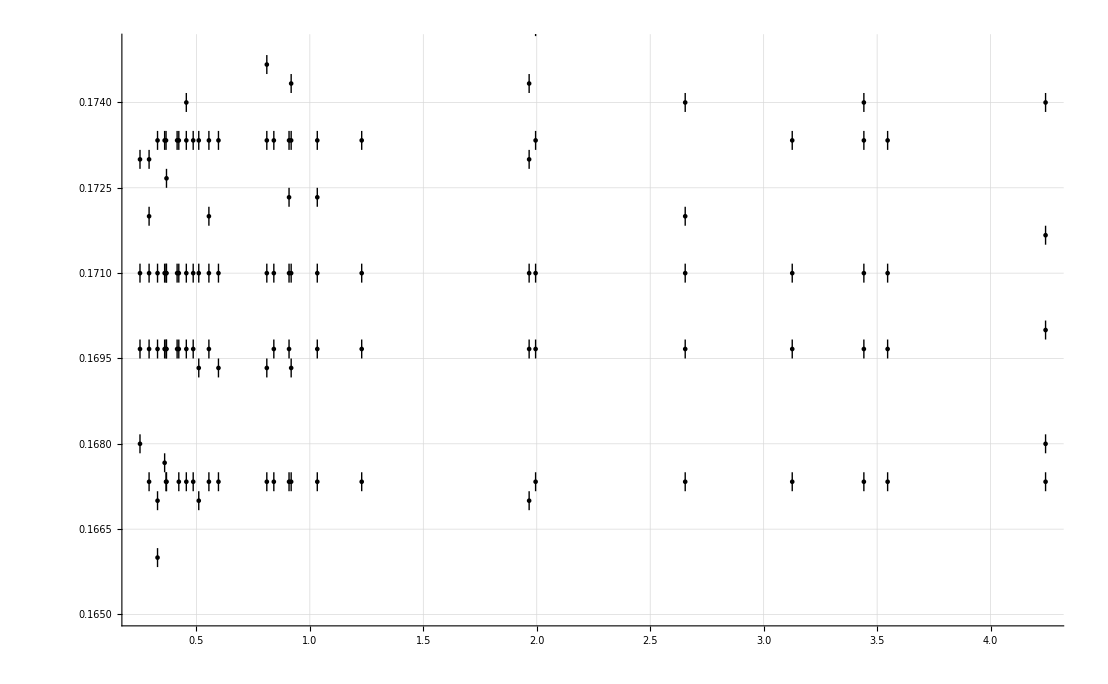

```mathematica
Show[Table[ListPlot[Table[{findAmplitude[i,500,-1.9],Around[findNthMax[i,0.155,0.185,3000,j,0],0.5/3000]},{i,1,26}],PlotStyle->Directive[PointSize[0.003],Black]],{j,1,5}],PlotRange->{0.165,0.175},GridLines->Automatic]
```

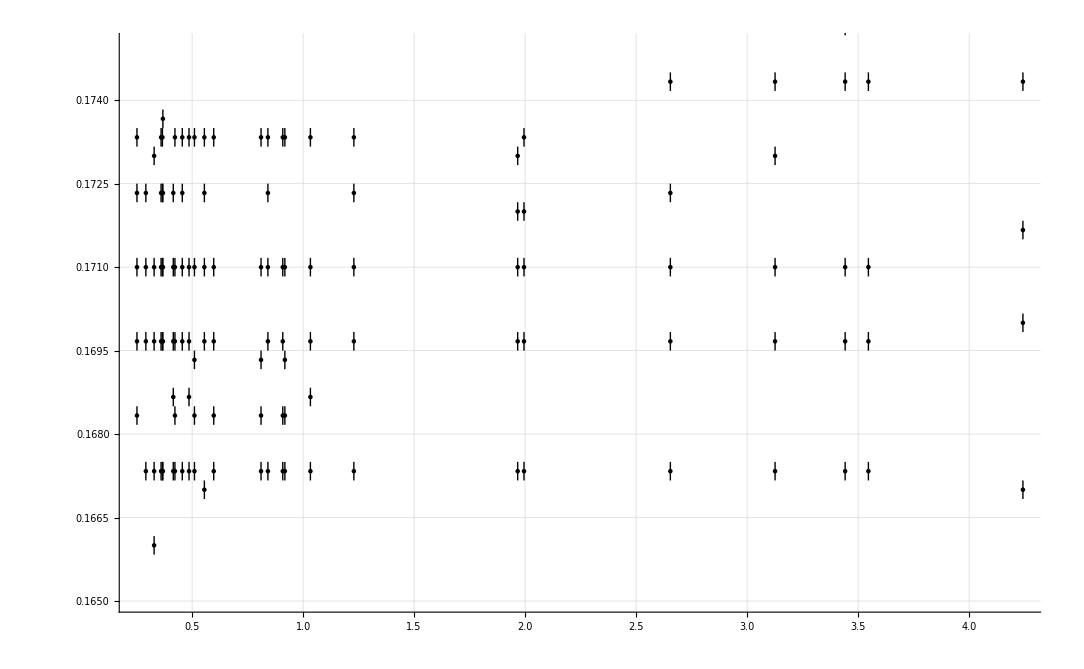

```mathematica
Show[Table[ListPlot[Table[{findAmplitude[i,500,-1.9],Around[findNthMax[i,0.155,0.185,3000,j,1],0.5/3000]},{i,1,26}],PlotStyle->Directive[PointSize[0.003],Black]],{j,1,5}],PlotRange->{0.165,0.175},GridLines->Automatic]
```

```mathematica
tunesX=Plot[Table[0.171+i 0.00245,{i,-1,1}],{x,0,4.4},PlotStyle->Red];
tunesY=Plot[Table[0.16972+i 0.00245,{i,-1,1}],{x,0,4.4},PlotStyle->Blue];
```

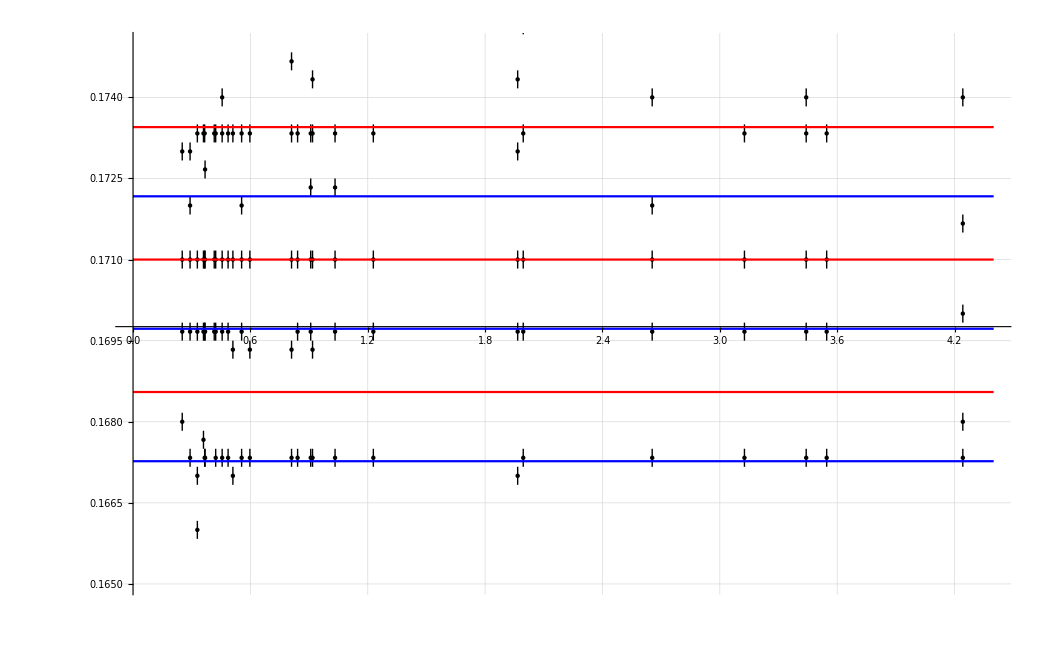

```mathematica
Show[{%33,tunesX,tunesY}]
```

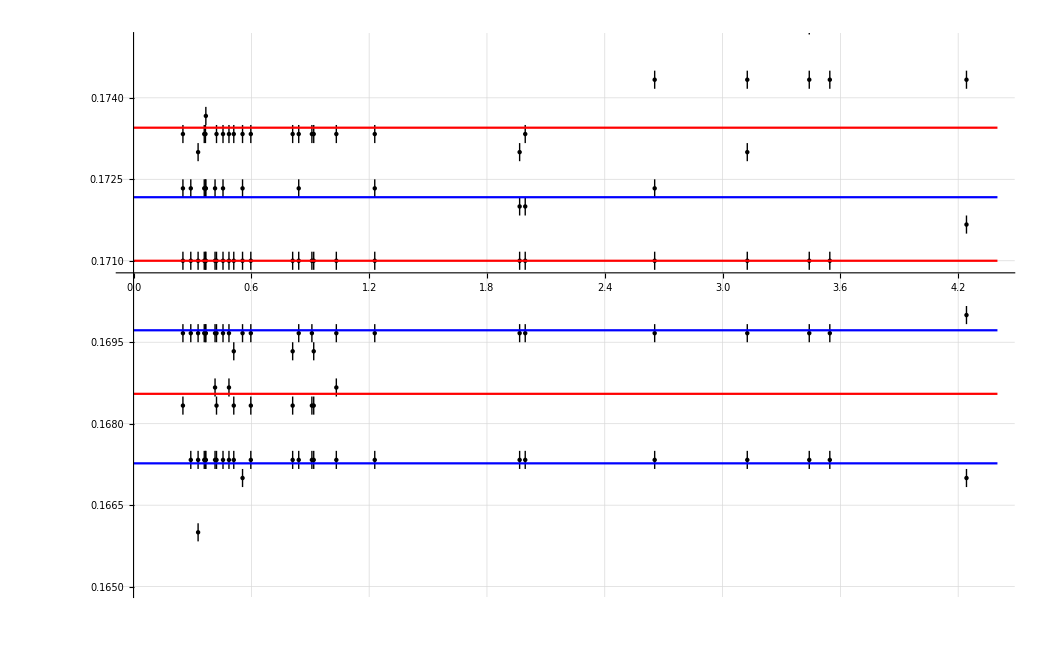

```mathematica
Show[{%34,tunesX,tunesY}]
```

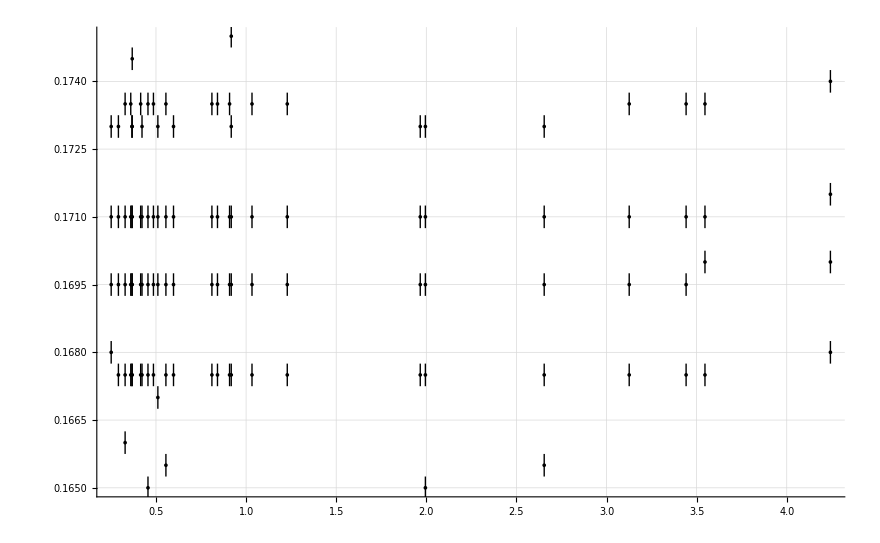

```mathematica
Show[Table[ListPlot[Table[{findAmplitude[i,500,-1.9],Around[findNthMax[i,0.155,0.185,2000,j,0],0.5/2000]},{i,1,26}],PlotStyle->Directive[PointSize[0.003],Black]],{j,1,5}],PlotRange->{0.165,0.175},GridLines->Automatic]
```

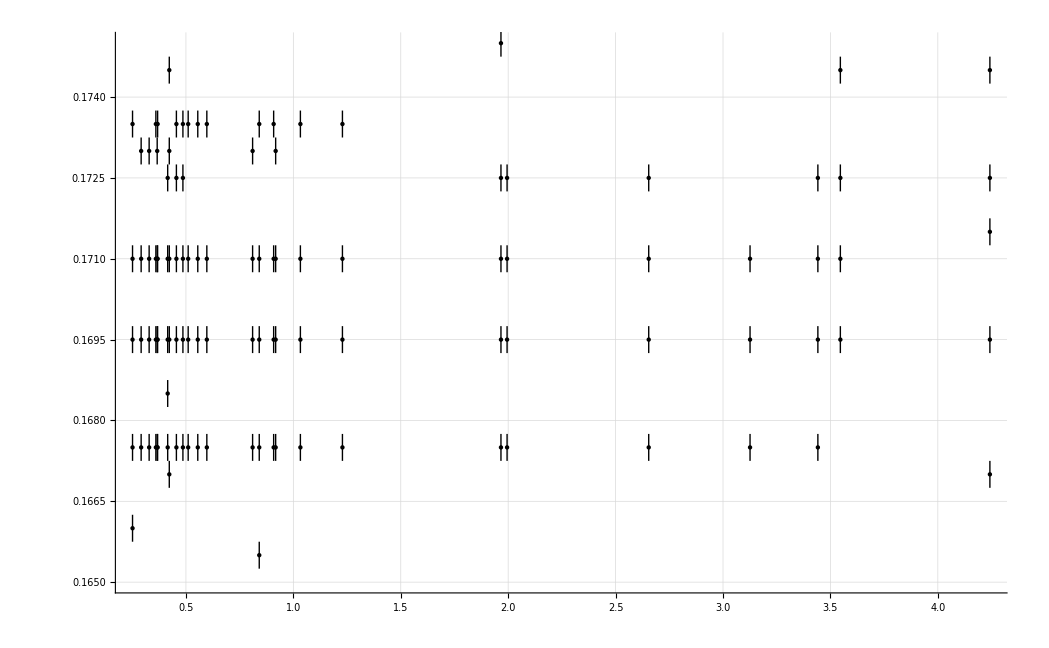

```mathematica
Show[Table[ListPlot[Table[{findAmplitude[i,500,-1.9],Around[findNthMax[i,0.155,0.185,2000,j,1],0.5/2000]},{i,1,26}],PlotStyle->Directive[PointSize[0.003],Black]],{j,1,5}],PlotRange->{0.165,0.175},GridLines->Automatic]
```

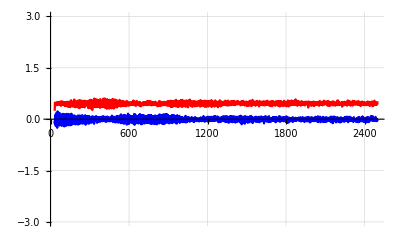

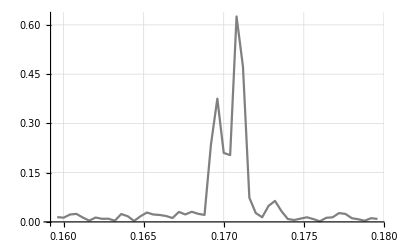

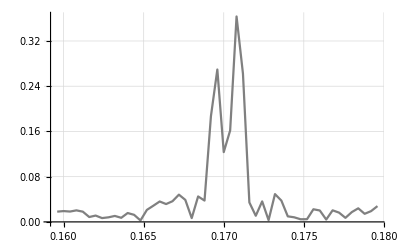

0.251477

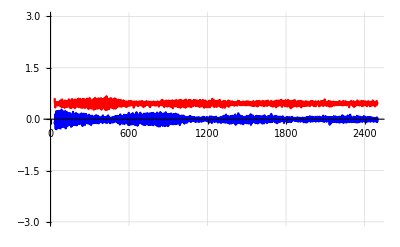

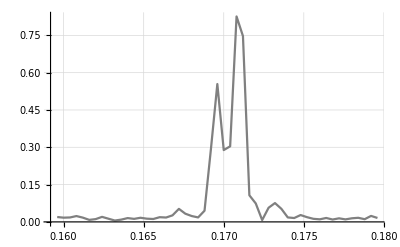

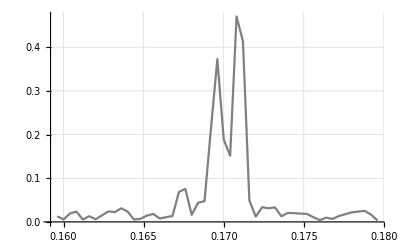

0.29155

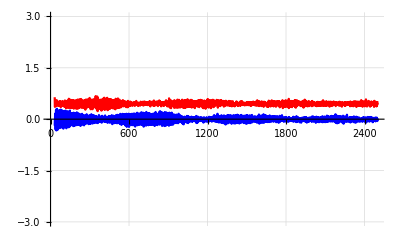

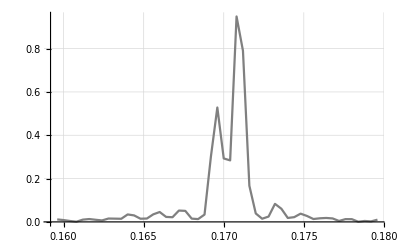

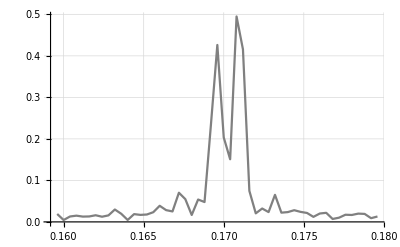

0.328779

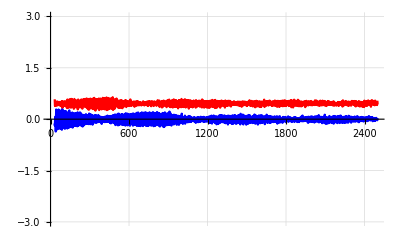

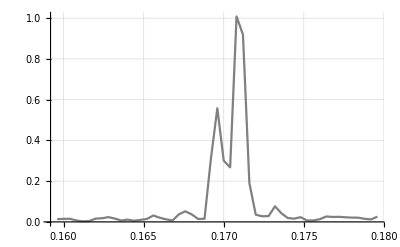

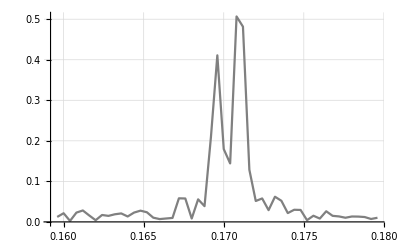

0.360083

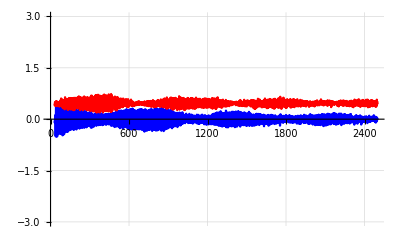

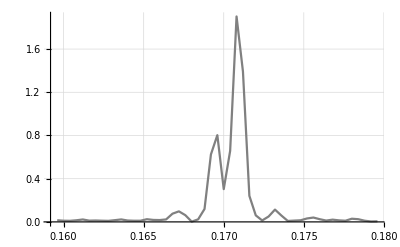

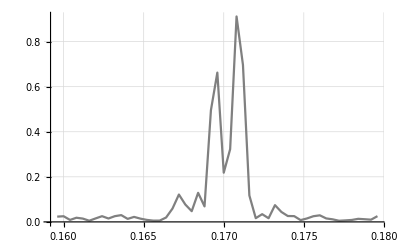

0.510477

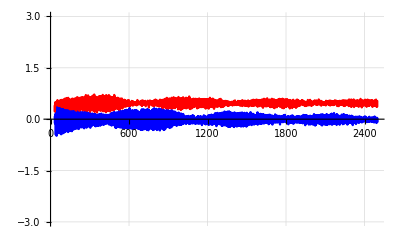

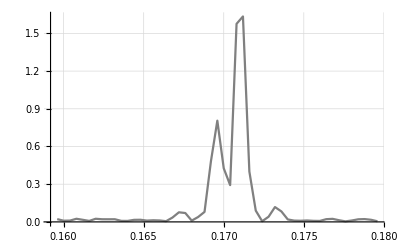

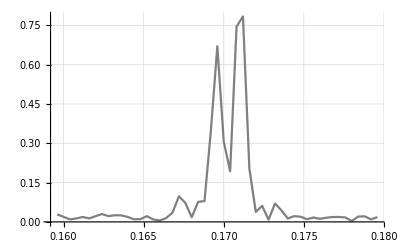

0.485965

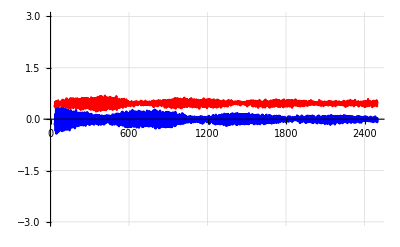

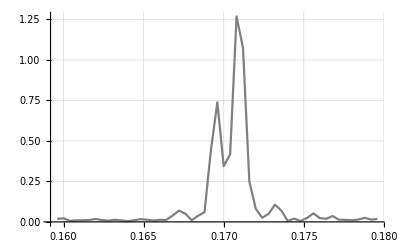

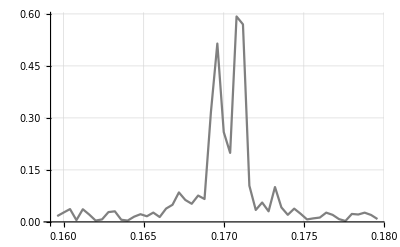

0.422528

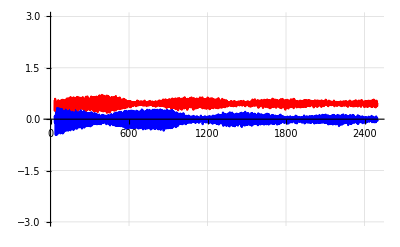

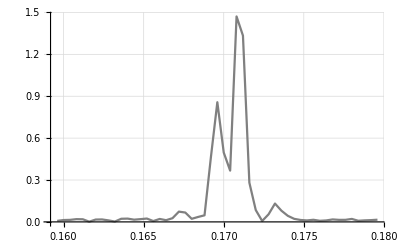

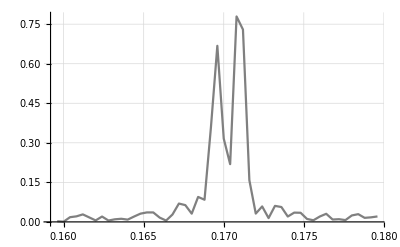

0.455632

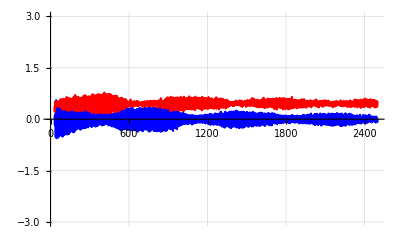

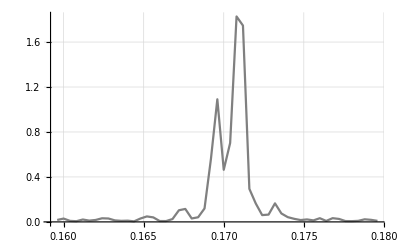

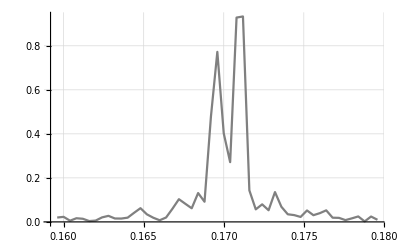

0.55514

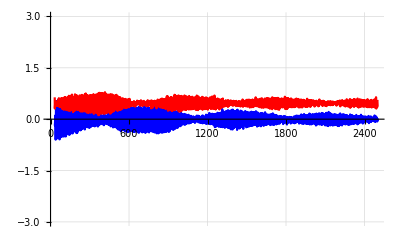

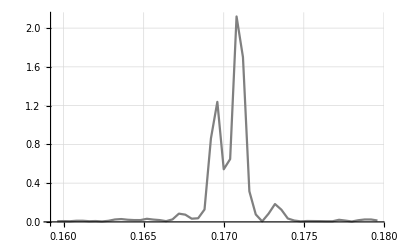

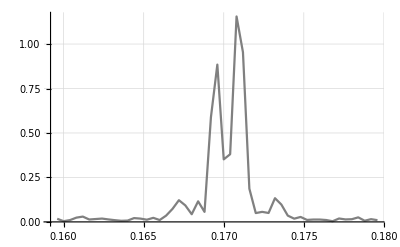

0.597305

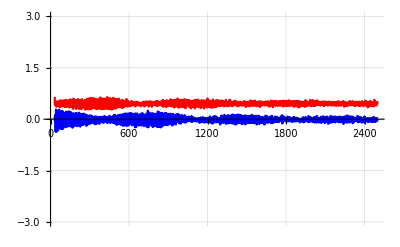

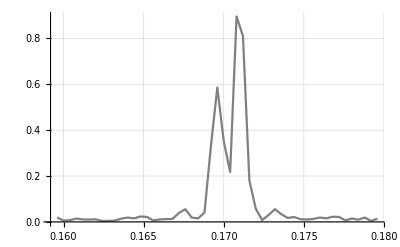

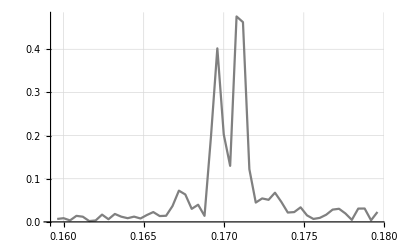

0.366228

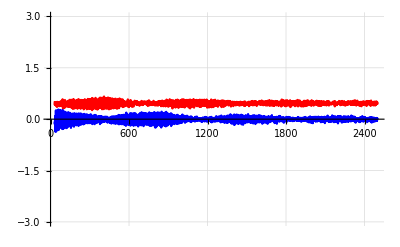

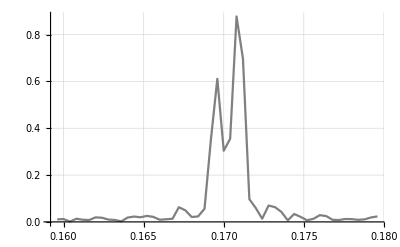

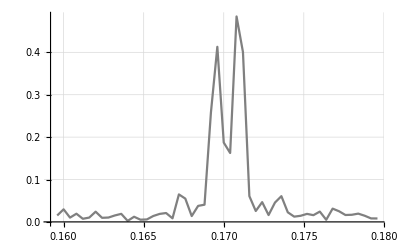

0.368251

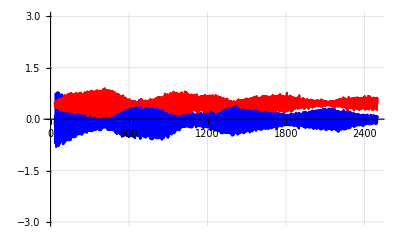

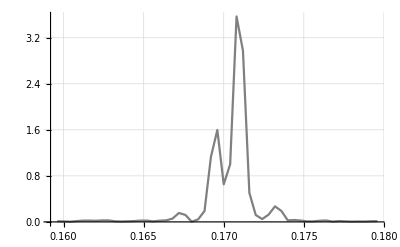

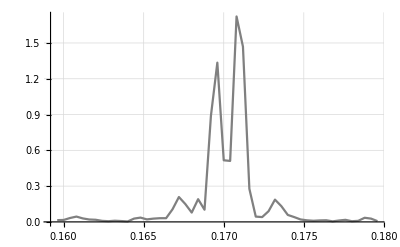

0.810372

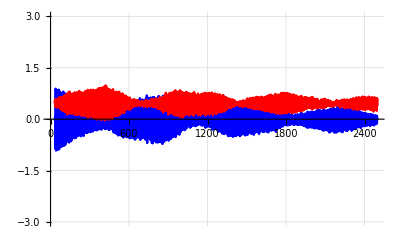

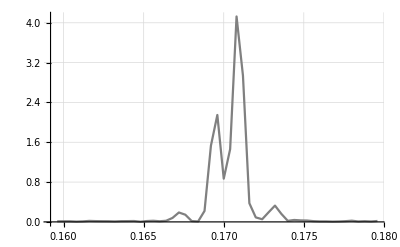

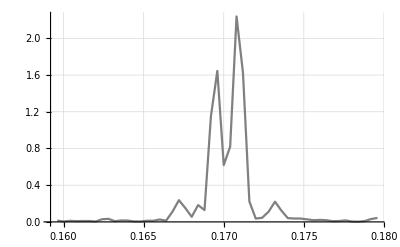

0.917676

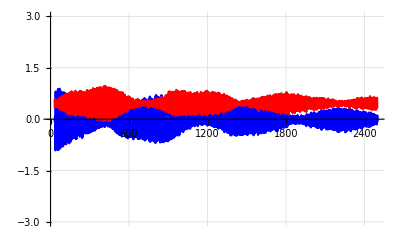

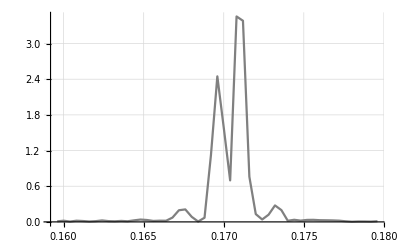

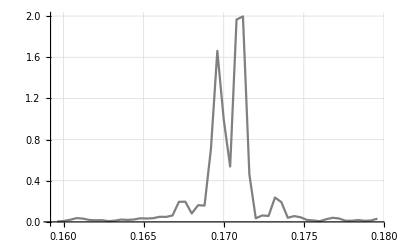

0.908336

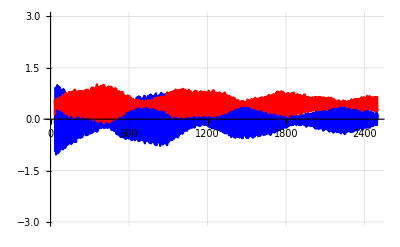

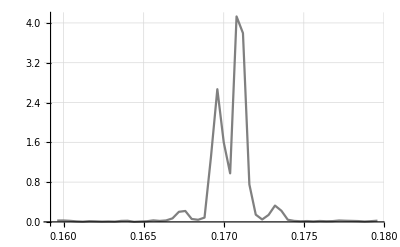

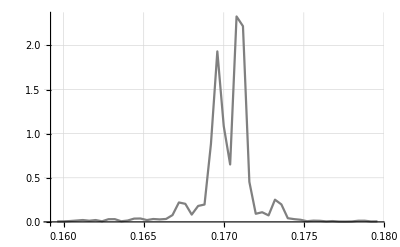

1.0328

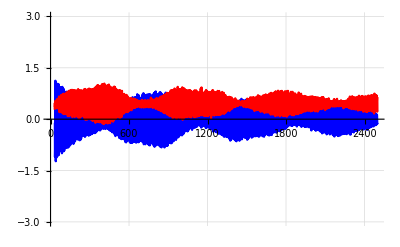

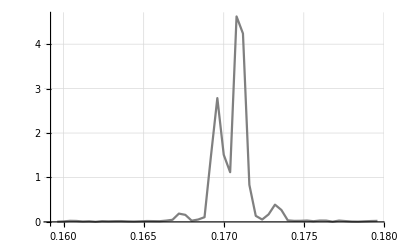

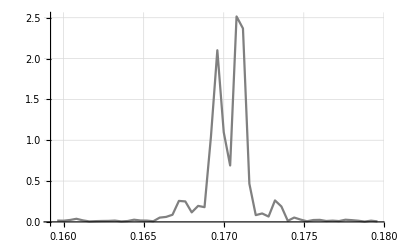

1.22852

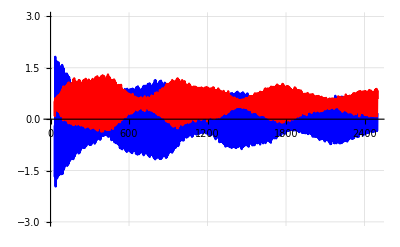

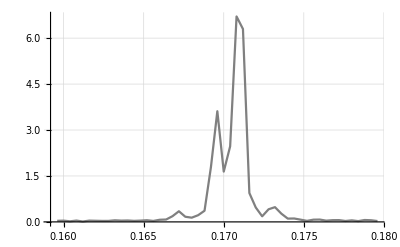

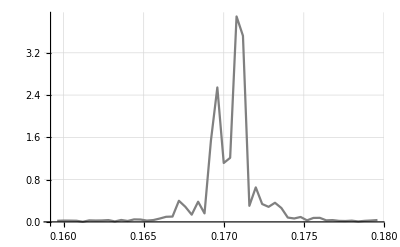

1.96641

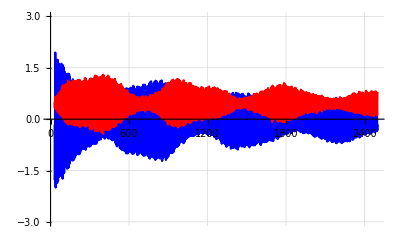

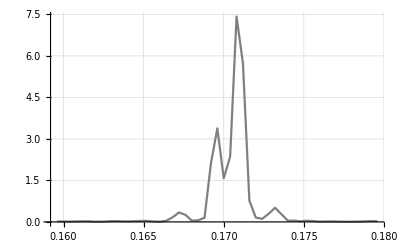

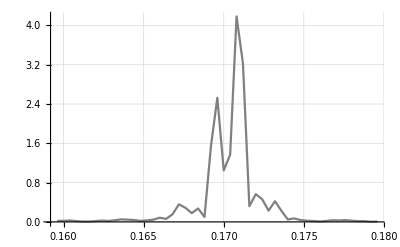

1.99489

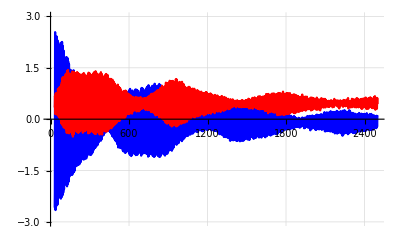

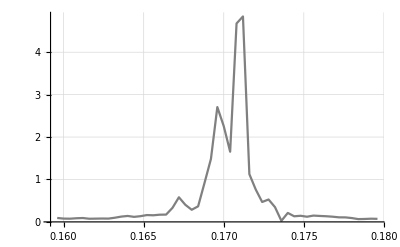

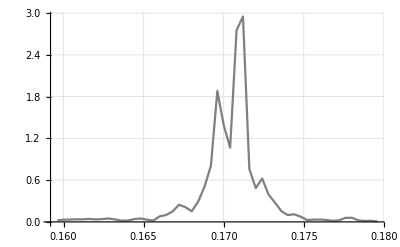

2.65419

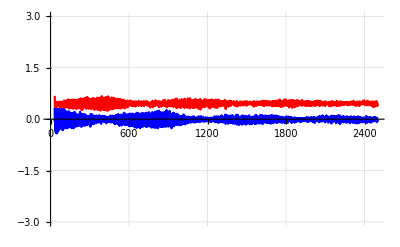

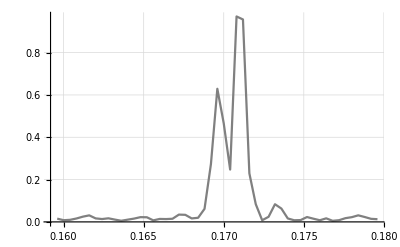

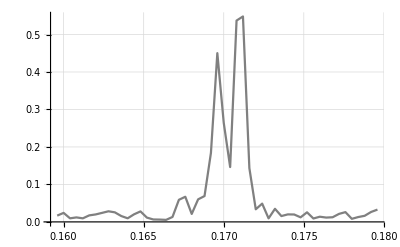

0.415092

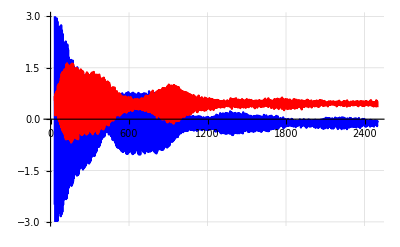

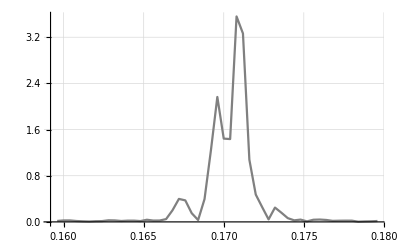

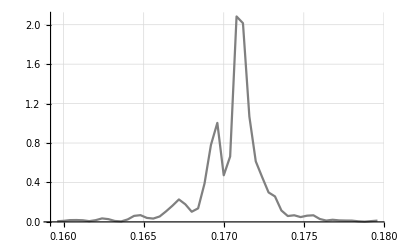

3.12586

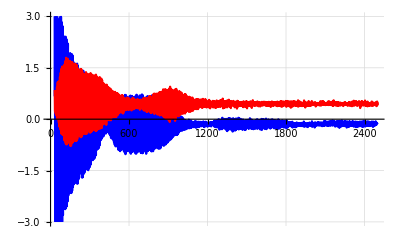

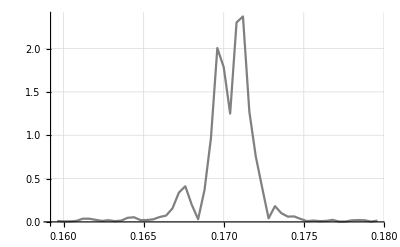

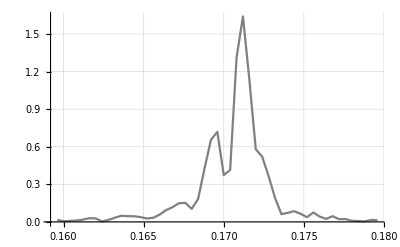

3.54624

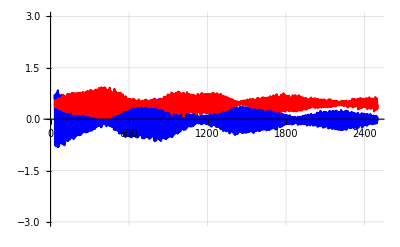

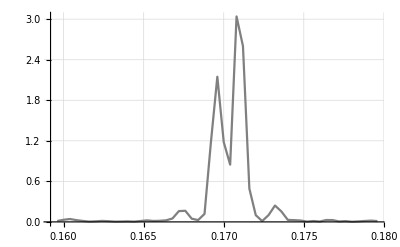

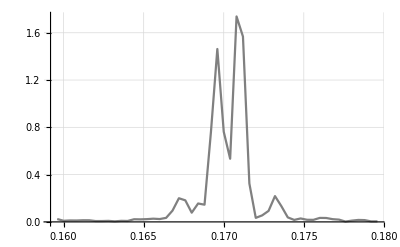

0.841292

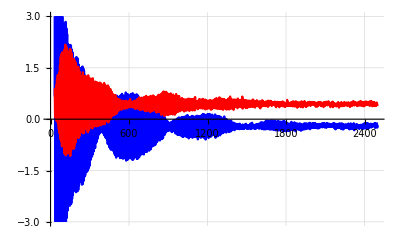

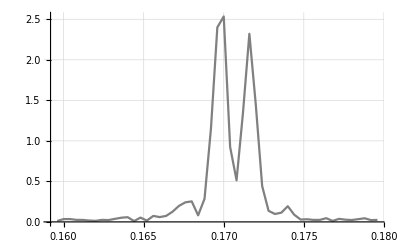

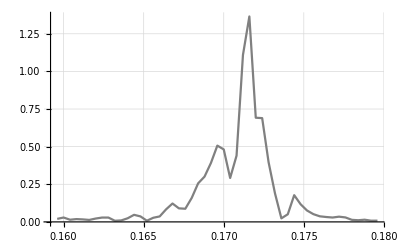

4.24231

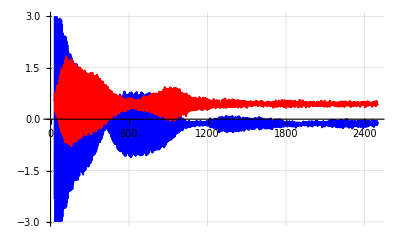

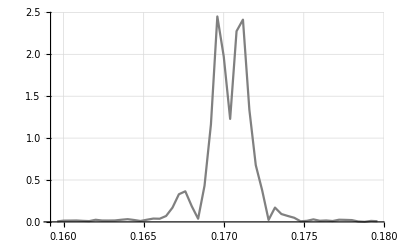

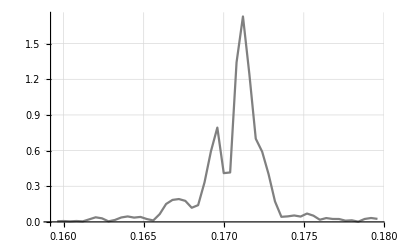

3.44155

```mathematica
Table[{plotHistory[i,2500,-1.9],plotFourier[i,0.16,0.18,2500,0],plotAmplitude[i,500,-1.9]},{i,1,26}];
```

```mathematica
(*e+, 3.5mA left after the slow dying from 120mA, νs = 0.0025, larger η*)
```

```mathematica
dataDirectory="C:\\D\WorkDirectory\\binp\\Mathematica\\pickup_data\\positrons\\";
```

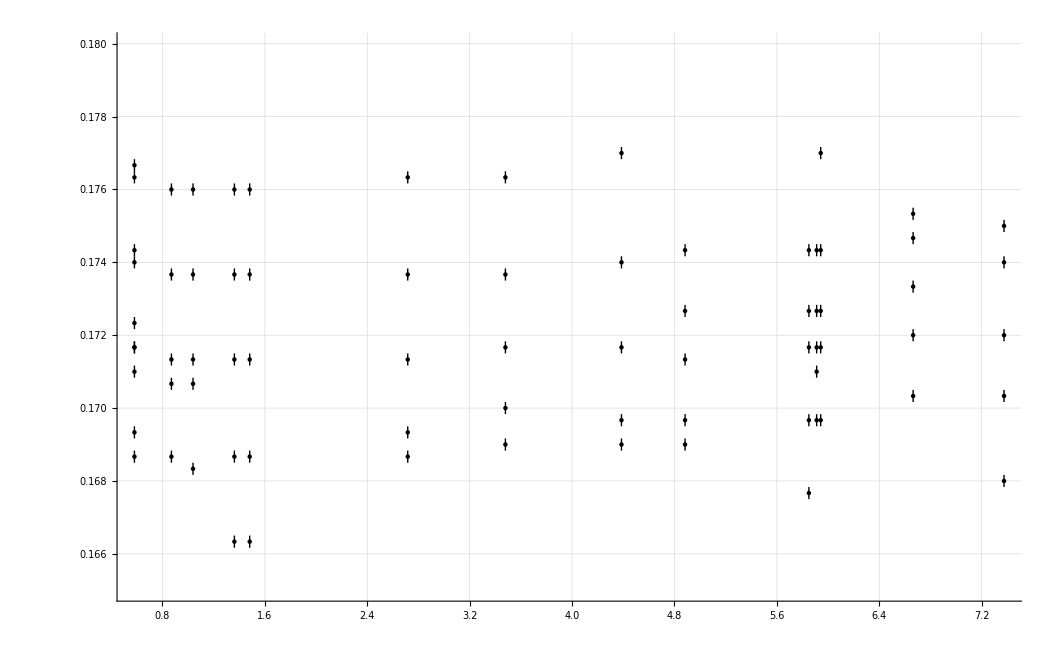

```mathematica
Show[Table[ListPlot[Table[{findAmplitude[i,500,-1.9],Around[findNthMax[i,0.165,0.18,3000,j,0],0.5/3000]},{i,1,15}],PlotStyle->Directive[PointSize[0.003],Black]],{j,1,5}],PlotRange->{0.165,0.18},GridLines->Automatic]
```

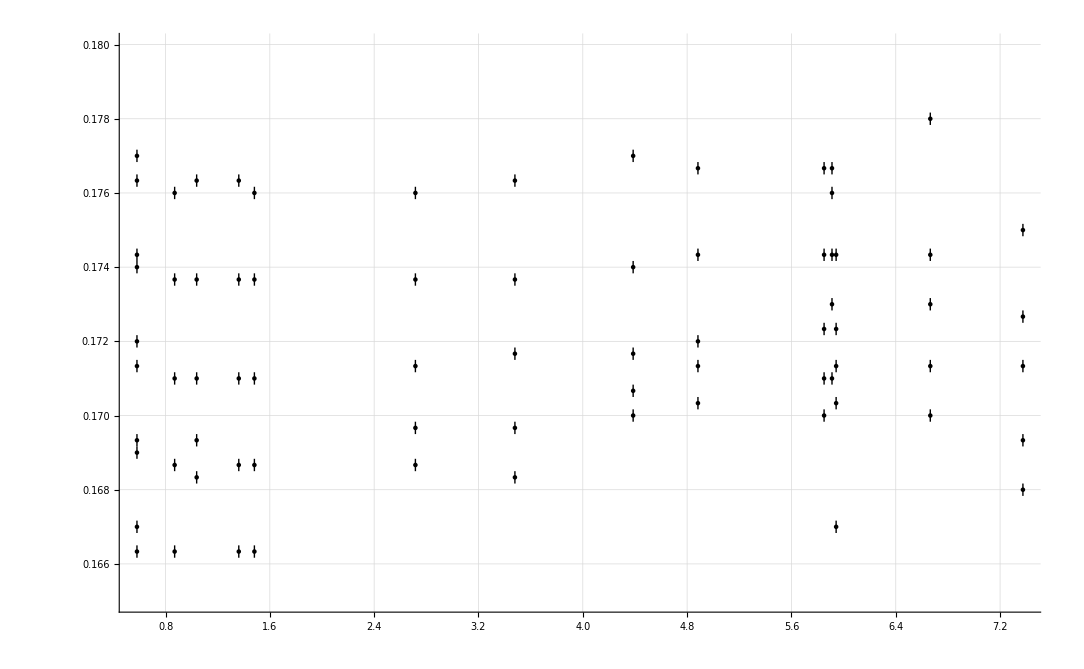

```mathematica
Show[Table[ListPlot[Table[{findAmplitude[i,500,-1.9],Around[findNthMax[i,0.165,0.18,3000,j,1],0.5/3000]},{i,1,15}],PlotStyle->Directive[PointSize[0.003],Black]],{j,1,5}],PlotRange->{0.165,0.18},GridLines->Automatic]
```

```mathematica
tunesX=Plot[Table[0.1739+i 0.00245,{i,-1,1}],{x,0,4.4},PlotStyle->Red];
tunesY=Plot[Table[0.1688+i 0.00245,{i,-1,1}],{x,0,4.4},PlotStyle->Blue];
```

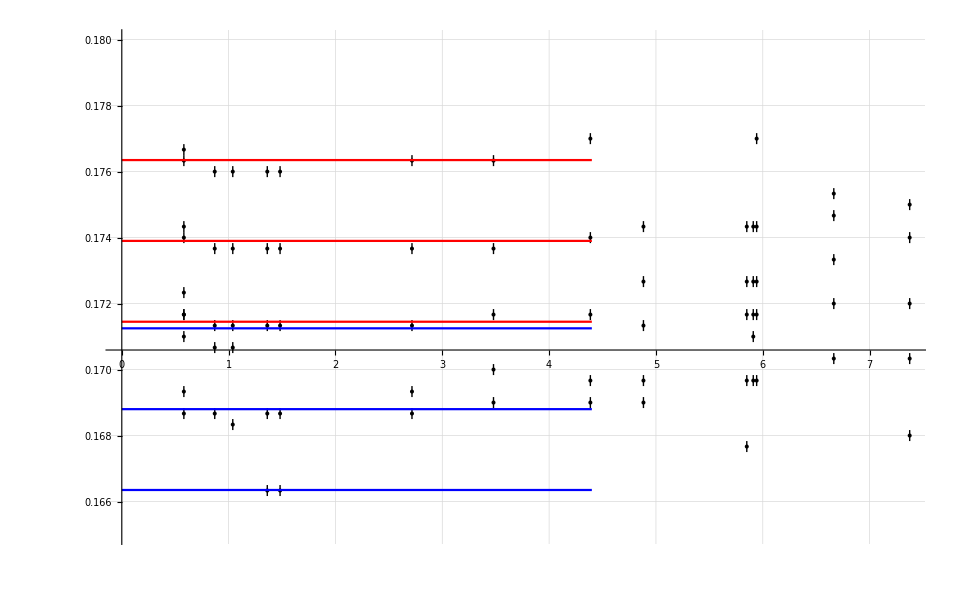

```mathematica
Show[{%82,tunesX,tunesY}]
```

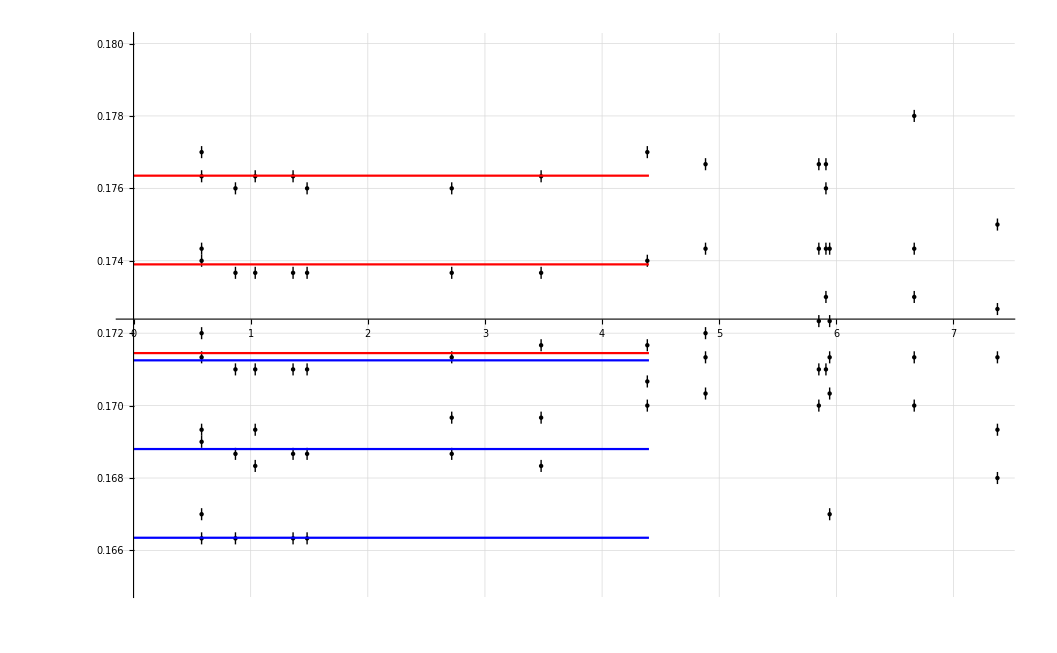

```mathematica
Show[{%83,tunesX,tunesY}]
```

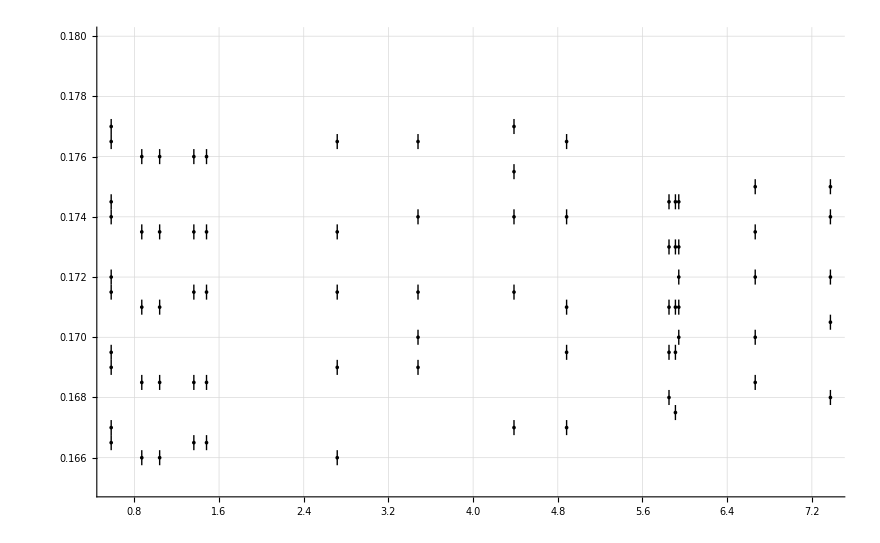

```mathematica
Show[Table[ListPlot[Table[{findAmplitude[i,500,-1.9],Around[findNthMax[i,0.165,0.18,2000,j,0],0.5/2000]},{i,1,15}],PlotStyle->Directive[PointSize[0.003],Black]],{j,1,5}],PlotRange->{0.165,0.18},GridLines->Automatic]
```

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

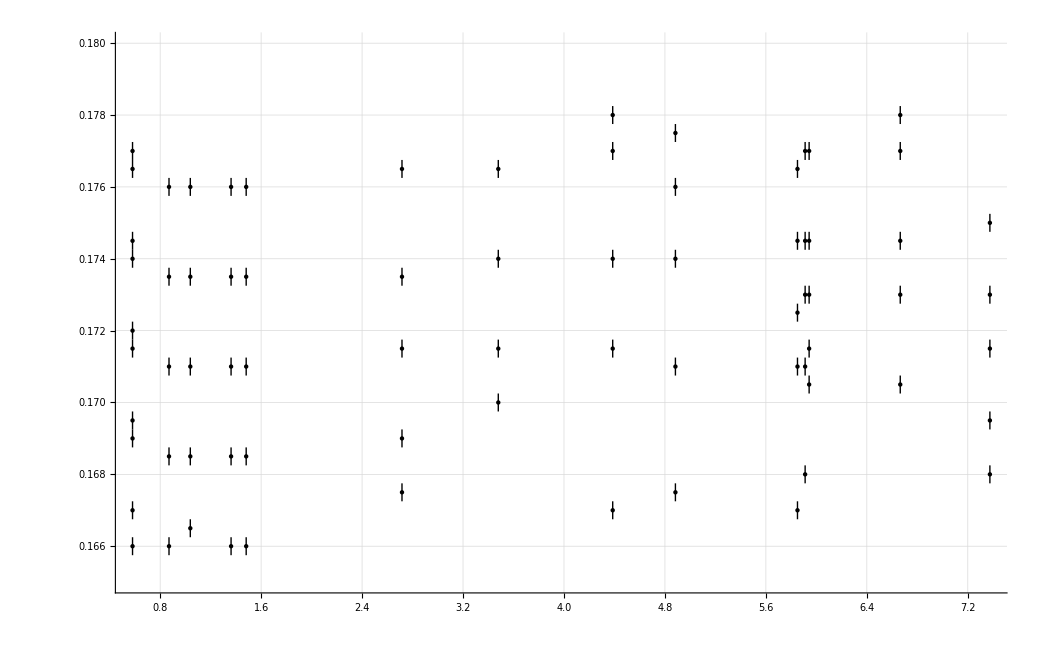

```mathematica
Show[Table[ListPlot[Table[{findAmplitude[i,500,-1.9],Around[findNthMax[i,0.165,0.18,2000,j,1],0.5/2000]},{i,1,15}],PlotStyle->Directive[PointSize[0.003],Black]],{j,1,5}],PlotRange->{0.165,0.18},GridLines->Automatic]
```

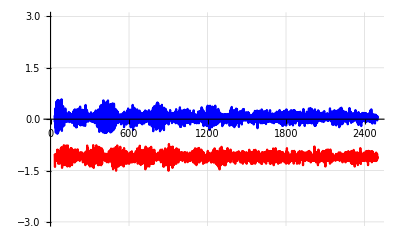

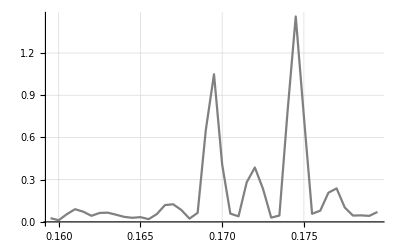

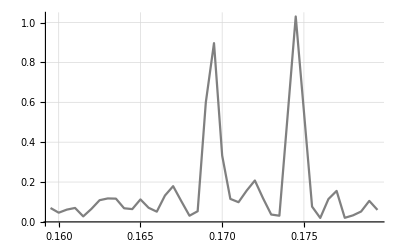

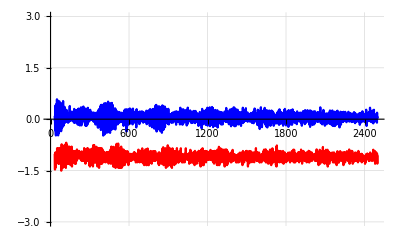

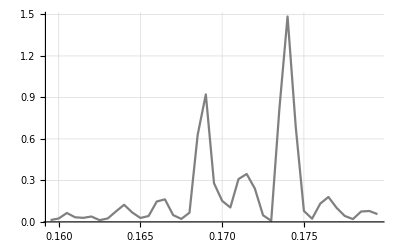

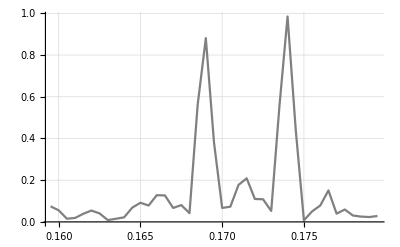

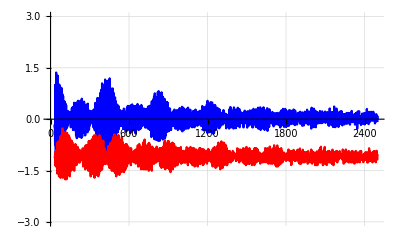

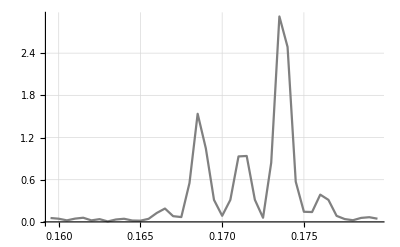

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

```mathematica
Table[{plotHistory[i,2500,-1.9],plotFourier[i,0.16,0.18,2000,0],findAmplitude[i,500,-1.9]},{i,1,15}];
```

```mathematica
(*2020: 970 MeV*)
```

```mathematica
dataDirectory="C:\\D\WorkDirectory\\binp\\Mathematica\\pickup_data\\2020\\";
```

```mathematica
Table[{plotHistory[i,2500,-0.3],plotFourier[i,0.16,0.22,3000,0],plotAmplitude[i,500,-0.35]},{i,{1,2,3,4,6,8,10,11,12,13}}];
```

-Graphics-

-Graphics-

-Graphics-

1.06715

-Graphics-

-Graphics-

-Graphics-

0.216395

-Graphics-

-Graphics-

-Graphics-

0.914367

-Graphics-

-Graphics-

-Graphics-

1.76389

-Graphics-

-Graphics-

-Graphics-

2.49828

-Graphics-

-Graphics-

-Graphics-

2.91791

-Graphics-

-Graphics-

-Graphics-

3.68783

-Graphics-

-Graphics-

-Graphics-

3.32489

-Graphics-

-Graphics-

-Graphics-

4.85047

-Graphics-

-Graphics-

-Graphics-

6.23154

```mathematica
Show[Table[ListPlot[Table[{findAmplitude[i,500,-0.3],Around[findNthMax[i,0.165,0.18,3000,j,0],0.5/3000]},{i,{1,2,3,4,6,8,10,11,12,13}}],PlotStyle->Directive[PointSize[0.003],Black]],{j,1,4}],PlotRange->{0.165,0.18},GridLines->Automatic]
```

-Graphics-

```mathematica
Show[Table[ListPlot[Table[{findAmplitude[i,500,-0.3],Around[findNthMax[i,0.165,0.18,3000,j,1],0.5/3000]},{i,{1,2,3,4,6,8,10,11,12,13}}],PlotStyle->Directive[PointSize[0.003],Black]],{j,1,4}],PlotRange->{0.165,0.18},GridLines->Automatic]
```

-Graphics-

```mathematica
tunesX=Plot[Table[0.1710+i 0.00265,{i,-1,1}],{x,0,4.4},PlotStyle->Red];
tunesY=Plot[Table[0.1703+i 0.00265,{i,-1,1}],{x,0,4.4},PlotStyle->Blue];
```

```mathematica
Show[{%17,tunesX,tunesY}]
```

-Graphics-

```mathematica
Show[{%18,tunesX,tunesY}]
```

-Graphics-

```mathematica
(*intensive beams: 26-26, 37-37, 62-62*)
```

```mathematica
intensities={26,37,62};
```

```mathematica
dataDirectory="C:\\D\WorkDirectory\\binp\\Mathematica\\pickup_data\\intensiveBeams\\";
```

```mathematica
Table[{plotHistory[i,2500,-1.9],plotFourier[i,0.16,0.22,1500,0],plotAmplitude[i,500,-1.9]},{i,1,3}];
```

-Graphics-

-Graphics-

-Graphics-

2.28524

-Graphics-

-Graphics-

-Graphics-

2.56991

-Graphics-

-Graphics-

-Graphics-

1.95495

```mathematica
Show[Table[ListPlot[Table[{findAmplitude[i,500,-1.9],findNthMax[i,0.2,0.21,4000,j,0]},{i,1,3}]],{j,1,6}],PlotRange->{0.2,0.21},GridLines->Automatic]
```

-Graphics-

```mathematica
Show[Table[ListPlot[Table[{intensities[[i]],findNthMax[i,0.185,0.21,4000,j,0]},{i,1,3}]],{j,1,5}],PlotRange->{0.185,0.21},GridLines->Automatic,LabelStyle->Directive[Medium,Bold]]
```

-Graphics-

```mathematica
Show[Table[ListPlot[Table[{intensities[[i]],findNthMax[i,0.165,0.21,2000,j,1]},{i,1,3}]],{j,1,8},AxesOrigin->{0,0.171}],PlotRange->{{0,65},{0.165,0.21}},GridLines->Automatic,LabelStyle->Directive[Medium,Bold]]
```

-Graphics-